```mathematica
<<xAct`xCoba`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.4, {2025,12,29}

CopyRight (C) 2003-2026, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor` version 1.3.0, {2025,12,29}

CopyRight (C) 2002-2026, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2026, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
<<xAct`TexAct`
```

------------------------------------------------------------

Package xAct`TexAct`  version 0.4.5, {2025,8,9}

CopyRight (C) 2008-2021, Thomas Bäckdahl, Jose M. Martin-Garcia and Barry Wardell, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
DefManifold[M,4,IndexRange[a,n]]
```

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

```mathematica
DefChart[ch,M,{0,1,2,3},{t[],r[],θ[],ϕ[]},ChartColor->Blue]
```

** DefChart: Defining chart ch.

** DefTensor: Defining coordinate scalar t[].

** DefTensor: Defining coordinate scalar r[].

** DefTensor: Defining coordinate scalar θ[].

** DefTensor: Defining coordinate scalar ϕ[].

** DefMapping: Defining mapping ch.

** DefMapping: Defining inverse mapping ich.

** DefTensor: Defining mapping differential tensor dich[-a,icha].

** DefTensor: Defining mapping differential tensor dch[-a,cha].

** DefBasis: Defining basis ch. Coordinated basis.

** DefCovD: Defining parallel derivative PDch[-a].

** DefTensor: Defining vanishing torsion tensor TorsionPDch[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDch[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDch[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDch[-a,-b].

** DefTensor: Defining antisymmetric +1 density etaUpch[a,b,c,d].

** DefTensor: Defining antisymmetric -1 density etaDownch[-a,-b,-c,-d].

```mathematica
DefScalarFunction[α]
```

** DefScalarFunction: Defining scalar function α.

```mathematica
DefScalarFunction[A]
```

** DefScalarFunction: Defining scalar function A.

```mathematica
(*Define Metric*)
```

```mathematica
met=CTensor[{{-α[t[],r[]]^2,0,0,0},{0,A[t[],r[]]^2,0,0},{0,0,r[]^2,0},{0,0,0,r[]^2 Sin[θ[]]^2}},{-ch,-ch}]
```

CTensor[{{-α[t,r]^2,0,0,0},{0,A[t,r]^2,0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}},{-ch,-ch},0]

```mathematica
SetCMetric[met,ch,SignatureOfMetric->{3,1,0}]
```

```mathematica
cd=CovDOfMetric[met];
```

```mathematica
MetricCompute[met,ch,All]
```

```mathematica
(* Define Christoffel Symbols*)
```

```mathematica
chr = Christoffel[cd,PDch];
```

```mathematica
(*Define Stress-Energy Tensor*)
```

```mathematica
DefTensor[T[a,b],M]
```

** DefTensor: Defining tensor T[a,b].

```mathematica
(* Define lapse*)
```

```mathematica
lapse = α[t[],r[]]
```

α[t,r]

```mathematica
Sum[chr[{a,ch},{a,-ch},{0,-ch}],{a,0,3}]//FullSimplify
```

(A^(1,0)[t,r])/A[t,r]+(α^(1,0)[t,r])/α[t,r]

```mathematica
Sum[chr[{a,ch},{a,-ch},{1,-ch}],{a,0,3}]//FullSimplify
```

2/r+(A^(0,1)[t,r])/A[t,r]+(α^(0,1)[t,r])/α[t,r]

```mathematica
Determinant[met,ch][]
```

OverTilde[OverTilde[-A[t,r]^2 r^4 Sin[θ]^2 α[t,r]^2]]

```mathematica
D[Log[A[t,r] r^2 Sin[θ] α[t,r]],t[]]//FullSimplify
```

(A^(1,0)[t,r])/A[t,r]+(α^(1,0)[t,r])/α[t,r]

```mathematica
D[Log[A[t,r] r^2 Sin[θ] α[t,r]],r[]]//FullSimplify
```

2/r+(A^(0,1)[t,r])/A[t,r]+(α^(0,1)[t,r])/α[t,r]

## Stress-Energy Tensor Definitions

```mathematica
RuleTSwap = {T[{0,ch},{0,ch}]->1/α[t[],r[]]^2(ρ[t[],r[]]+p[t[],r[]])*Γ[t[],r[]]^2+p[t[],r[]]*met[{0,ch},{0,ch}],

T[{0,ch},{1,ch}]->1/(α[t[],r[]]*A[t[],r[]])(ρ[t[],r[]]+p[t[],r[]])*Γ[t[],r[]]^2*v[t[],r[]],
T[{1,ch},{0,ch}]->1/(α[t[],r[]]*A[t[],r[]])(ρ[t[],r[]]+p[t[],r[]])*Γ[t[],r[]]^2*v[t[],r[]],
T[{0,ch},{2,ch}]->0,
T[{0,ch},{3,ch}]->0,
T[{2,ch},{0,ch}]->0,
T[{3,ch},{0,ch}]->0,
T[{1,ch},{1,ch}]->1/A[t[],r[]]^2(ρ[t[],r[]]+p[t[],r[]])*Γ[t[],r[]]^2*v[t[],r[]]^2+p[t[],r[]]*met[{1,ch},{1,ch}],
T[{1,ch},{2,ch}]->0,
T[{1,ch},{3,ch}]->0,
T[{2,ch},{1,ch}]->0,
T[{3,ch},{1,ch}]->0,
T[{2,ch},{2,ch}]->p[t[],r[]]*met[{2,ch},{2,ch}],
T[{2,ch},{3,ch}]->p[t[],r[]]*met[{2,ch},{3,ch}],
T[{3,ch},{2,ch}]->p[t[],r[]]*met[{3,ch},{2,ch}],
T[{3,ch},{3,ch}]->p[t[],r[]]*met[{3,ch},{3,ch}]}//FullSimplify
```

{T | 0 | 0
  |  →(-p[t,r]+Γ[t,r]^2 (p[t,r]+ρ[t,r]))/α[t,r]^2,T | 0 | 1
  |  →(v[t,r] Γ[t,r]^2 (p[t,r]+ρ[t,r]))/(A[t,r] α[t,r]),T | 1 | 0
  |  →(v[t,r] Γ[t,r]^2 (p[t,r]+ρ[t,r]))/(A[t,r] α[t,r]),T | 0 | 2
  |  →0,T | 0 | 3
  |  →0,T | 2 | 0
  |  →0,T | 3 | 0
  |  →0,T | 1 | 1
  |  →(p[t,r]+v[t,r]^2 Γ[t,r]^2 (p[t,r]+ρ[t,r]))/A[t,r]^2,T | 1 | 2
  |  →0,T | 1 | 3
  |  →0,T | 2 | 1
  |  →0,T | 3 | 1
  |  →0,T | 2 | 2
  |  →p[t,r]/r^2,T | 2 | 3
  |  →0,T | 3 | 2
  |  →0,T | 3 | 3
  |  →(Csc[θ]^2 p[t,r])/r^2}

```mathematica
RuleTSwapDown = {T[{0,-ch},{0,-ch}]->(1/α[t[],r[]]^2(ρ[t[],r[]]+p[t[],r[]])*Γ[t[],r[]]^2+p[t[],r[]]*met[{0,ch},{0,ch}])*met[{0,-ch},{0,-ch}]^2,

T[{0,-ch},{1,-ch}]->(1/(α[t[],r[]]*A[t[],r[]])(ρ[t[],r[]]+p[t[],r[]])*Γ[t[],r[]]^2*v[t[],r[]])*met[{0,-ch},{0,-ch}]*met[{1,-ch},{1,-ch}],
T[{1,-ch},{0,-ch}]->(1/(α[t[],r[]]*A[t[],r[]])(ρ[t[],r[]]+p[t[],r[]])*Γ[t[],r[]]^2*v[t[],r[]])*met[{0,-ch},{0,-ch}]*met[{1,-ch},{1,-ch}],
T[{0,-ch},{2,-ch}]->0,
T[{0,-ch},{3,-ch}]->0,
T[{2,-ch},{0,-ch}]->0,
T[{3,-ch},{0,-ch}]->0,
T[{1,-ch},{1,-ch}]->(1/A[t[],r[]]^2(ρ[t[],r[]]+p[t[],r[]])*Γ[t[],r[]]^2*v[t[],r[]]^2+p[t[],r[]]*met[{1,ch},{1,ch}])*met[{1,-ch},{1,-ch}]*met[{1,-ch},{1,-ch}],
T[{1,-ch},{2,-ch}]->0,
T[{1,-ch},{3,-ch}]->0,
T[{2,-ch},{1,-ch}]->0,
T[{3,-ch},{1,-ch}]->0,
T[{2,-ch},{2,-ch}]->(p[t[],r[]]*met[{2,ch},{2,ch}])*met[{2,-ch},{2,-ch}]*met[{2,-ch},{2,-ch}],
T[{2,-ch},{3,-ch}]->(p[t[],r[]]*met[{2,ch},{3,ch}])*met[{2,-ch},{2,-ch}]*met[{3,-ch},{3,-ch}],
T[{3,-ch},{2,-ch}]->(p[t[],r[]]*met[{3,ch},{2,ch}])*met[{2,-ch},{2,-ch}]*met[{3,-ch},{3,-ch}],
T[{3,-ch},{3,-ch}]->(p[t[],r[]]*met[{3,ch},{3,ch}])*met[{3,-ch},{3,-ch}]*met[{3,-ch},{3,-ch}]}//FullSimplify
```

{T |   |  
0 | 0→α[t,r]^2 (p[t,r] (-1+Γ[t,r]^2)+Γ[t,r]^2 ρ[t,r]),T |   |  
0 | 1→-A[t,r] v[t,r] α[t,r] Γ[t,r]^2 (p[t,r]+ρ[t,r]),T |   |  
1 | 0→-A[t,r] v[t,r] α[t,r] Γ[t,r]^2 (p[t,r]+ρ[t,r]),T |   |  
0 | 2→0,T |   |  
0 | 3→0,T |   |  
2 | 0→0,T |   |  
3 | 0→0,T |   |  
1 | 1→A[t,r]^2 (p[t,r] (1+v[t,r]^2 Γ[t,r]^2)+v[t,r]^2 Γ[t,r]^2 ρ[t,r]),T |   |  
1 | 2→0,T |   |  
1 | 3→0,T |   |  
2 | 1→0,T |   |  
3 | 1→0,T |   |  
2 | 2→p[t,r] r^2,T |   |  
2 | 3→0,T |   |  
3 | 2→0,T |   |  
3 | 3→p[t,r] r^2 Sin[θ]^2}

## ADM Equations

Hamiltonian Constraint

```mathematica
HamiltonianEq = Flatten[Collect[Solve[Einstein[cd][{0,-ch},{0,-ch}]==T[{0,-ch},{0,-ch}]/.RuleTSwapDown//FullSimplify,Derivative[0,1][A][t,r]],r[],FullSimplify]]
```

{A^(0,1)[t,r]→-(A[t,r] (-1+A[t,r]^2))/(2 r)+1/2 A[t,r]^3 r (p[t,r] (-1+Γ[t,r]^2)+Γ[t,r]^2 ρ[t,r])}

Momentum Constraint

```mathematica
MomentumEq = Flatten[Collect[Solve[Einstein[cd][{0,-ch},{1,-ch}]==T[{0,-ch},{1,-ch}]/.RuleTSwapDown,Derivative[1,0][A][t,r]],r[],FullSimplify]]
```

{A^(1,0)[t,r]→-1/2 A[t,r]^2 r v[t,r] α[t,r] Γ[t,r]^2 (p[t,r]+ρ[t,r])}

Polar Slicing Condition (Enforced by choice of metric ansatz)

```mathematica
PolarEq = Flatten[Collect[Solve[Einstein[cd][{1,-ch},{1,-ch}]==T[{1,-ch},{1,-ch}]/.RuleTSwapDown,Derivative[0,1][α][t,r]],r[],FullSimplify]]
```

{α^(0,1)[t,r]→((-1+A[t,r]^2) α[t,r])/(2 r)+1/2 A[t,r]^2 r α[t,r] (p[t,r] (1+v[t,r]^2 Γ[t,r]^2)+v[t,r]^2 Γ[t,r]^2 ρ[t,r])}

## Euler Equations Source Terms

```mathematica
α[t[],r[]]^2(-Sum[chr[{a,ch},{a,-ch},{c,-ch}]*T[{0,ch},{c,ch}],{a,0,3},{c,0,3}]-Sum[chr[{0,ch},{a,-ch},{c,-ch}]*T[{a,ch},{c,ch}],{a,0,3},{c,0,3}]+2/α[t[],r[]]^3*D[α[t[],r[]],t[]]*((ρ[t[],r[]]+p[t[],r[]])*Γ[t[],r[]]^2-p[t[],r[]])+2/α[t[],r[]]^3*D[α[t[],r[]],r[]]*α[t[],r[]]/A[t[],r[]]*((ρ[t[],r[]]+p[t[],r[]])*Γ[t[],r[]]^2*v[t[],r[]]))/.RuleTSwap/.HamiltonianEq/.MomentumEq/.PolarEq/.Γ[t,r[]]->1/(√(1-v[t[],r[]]^2))//FullSimplify
```

(2 v[t,r] α[t,r] (p[t,r]+ρ[t,r]))/(A[t,r] r (-1+v[t,r]^2))

```mathematica
Collect[(A[t[],r[]]*α[t[],r[]])*(-Sum[chr[{a,ch},{a,-ch},{c,-ch}]*T[{1,ch},{c,ch}],{a,0,3},{c,0,3}]-Sum[chr[{1,ch},{a,-ch},{c,-ch}]*T[{a,ch},{c,ch}],{a,0,3},{c,0,3}]+1/(A[t[],r[]]*α[t[],r[]])^2*D[A[t[],r[]]*α[t[],r[]],t[]]*((ρ[t[],r[]]+p[t[],r[]])*Γ[t[],r[]]^2*v[t[],r[]])+1/(A[t[],r[]]*α[t[],r[]])^2*D[α[t[],r[]]*A[t[],r[]],r[]]*α[t[],r[]]/A[t[],r[]]*((ρ[t[],r[]]+p[t[],r[]])*Γ[t[],r[]]^2*v[t[],r[]]^2+p[t[],r[]]))/.RuleTSwap/.HamiltonianEq/.MomentumEq/.PolarEq/.Γ[t,r[]]->1/(√(1-v[t[],r[]]^2))//FullSimplify,r[],FullSimplify]
```

-A[t,r] p[t,r] r α[t,r] ρ[t,r]+(α[t,r] (p[t,r] (1+3 v[t,r]^2+A[t,r]^2 (-1+v[t,r]^2))+(-1+A[t,r]^2-(-5+A[t,r]^2) v[t,r]^2) ρ[t,r]))/(2 A[t,r] r (-1+v[t,r]^2))

```mathematica
Collect[-A[t,r] p[t,r] r α[t,r] ρ[t,r]+(α[t,r] (p[t,r] (1+3 v[t,r]^2+A[t,r]^2 (-1+v[t,r]^2))+(-1+A[t,r]^2-(-5+A[t,r]^2) v[t,r]^2) ρ[t,r]))/(2 A[t,r] r (-1+v[t,r]^2))==(-A[t,r] p[t,r] r α[t,r] ρ[t,r]+((A[t[],r[]]^2-1)*α[t[],r[]]*(p[t[],r[]]-ρ[t[],r[]]))/(2*A[t[],r[]]*r[])-2/r[] α[t[],r[]]/A[t[],r[]]((ρ[t[],r[]]+p[t[],r[]])*Γ[t[],r[]]^2*v[t[],r[]]^2))/.HamiltonianEq/.MomentumEq/.PolarEq/.Γ[t,r[]]->1/(√(1-v[t[],r[]]^2))//FullSimplify,r[],FullSimplify]//FullSimplify
```

True

```mathematica
(((K+1)ρ[t[],r[]]-1)*Γ[t[],r[]]^2*v[t[],r[]]^2)-(((K+1)ρ[t[],r[]]-1)*Γ[t[],r[]]^2-(K*ρ[t[],r[]]-1))/.Γ[t,r[]]->1/(√(1-v[t[],r[]]^2))//FullSimplify
```

-ρ[t,r]

## Primitive Recovery

```mathematica
S = (((K+1)ρ[t[],r[]]-1)*Γ[t[],r[]]^2*v[t[],r[]])
```

v[t,r] Γ[t,r]^2 (-1+(1+K) ρ[t,r])

```mathematica
τ=(((K+1)ρ[t[],r[]]-1)*Γ[t[],r[]]^2-(K*ρ[t[],r[]]-1))
```

1-K ρ[t,r]+Γ[t,r]^2 (-1+(1+K) ρ[t,r])

```mathematica
$Assumptions={0<K<=1,ρ[t[],r[]]>0,0<=v[t[],r[]]<1,(-1+(1+K) ρ[t,r])>0} (*Note that the last condition implies ρ+p>0*)
```

{0<K≤1,ρ[t,r]>0,0≤v[t,r]<1,-1+(1+K) ρ[t,r]>0}

```mathematica
(2*S)/(-1+τ+K τ+√((-1+τ+K τ)^2-4 K S^2))/.Γ[t,r[]]->1/(√(1-v[t[],r[]]^2))//FullSimplify
```

v[t,r]

```mathematica
(1+(-1+K) τ+√((-1+τ+K τ)^2-4 K S^2))/(2 K)/.Γ[t,r[]]->1/(√(1-v[t[],r[]]^2))//FullSimplify
```

ρ[t,r]

```mathematica
$Assumptions=ClearAll
```

ClearAll

Find bounds for physical densities/pressures:

```mathematica
Clear[S,τ]
```

```mathematica
Reduce[Exists[{ρ,v},0<K<=1&&ρ>1/K&&0<=v<1&&S==((K+1) ρ-1)/(1-v^2)*v&&τ==((K+1) ρ-1)/(1-v^2)-(K ρ-1)],{S,τ},Reals]
```

0<K≤1&&S≥0&&τ>1/(2 K)+1/2 √((1+4 K^2 S^2)/K^2)

## Characteristic Speeds/Eigenvectors

```mathematica
A0 = D[{1/(1-v^2)*(ρ+p[ρ])-p[ρ],1/(1-v^2)*(ρ+p[ρ])*v},{{ρ,v},1}]
```

{{-p'[ρ]+(1+p'[ρ])/(1-v^2),(2 v (ρ+p[ρ]))/((1-v^2)^2)},{(v (1+p'[ρ]))/(1-v^2),(2 v^2 (ρ+p[ρ]))/((1-v^2)^2)+(ρ+p[ρ])/(1-v^2)}}

```mathematica
A1 = D[α/a*{1/(1-v^2)*(ρ+p[ρ])*v,1/(1-v^2)*(ρ+p[ρ])*v^2+p[ρ]},{{ρ,v},1}]
```

{{(v α (1+p'[ρ]))/(a (1-v^2)),(2 v^2 α (ρ+p[ρ]))/(a (1-v^2)^2)+(α (ρ+p[ρ]))/(a (1-v^2))},{(α (p'[ρ]+(v^2 (1+p'[ρ]))/(1-v^2)))/a,(α ((2 v^3 (ρ+p[ρ]))/((1-v^2)^2)+(2 v (ρ+p[ρ]))/(1-v^2)))/a}}

```mathematica
F = A1.Inverse[A0]//FullSimplify
```

{{0,α/a},{(α (v^2-p'[ρ]))/(a (-1+v^2 p'[ρ])),(2 v α (-1+p'[ρ]))/(a (-1+v^2 p'[ρ]))}}

```mathematica
Eigenvalues[F]//FullSimplify
```

{(α (v-v p'[ρ]+√((-1+v^2)^2 p'[ρ])))/(a-a v^2 p'[ρ]),(α (v (-1+p'[ρ])+√((-1+v^2)^2 p'[ρ])))/(a (-1+v^2 p'[ρ]))}

```mathematica
((v-K v+√(K (-1+v^2)^2)) α)/(a-a K v^2)/.K->1
```

(√((-1+v^2)^2) α)/(a-a v^2)

```mathematica
(((-1+K) v+√(K (-1+v^2)^2)) α)/(a (-1+K v^2))/.K->1
```

(√((-1+v^2)^2) α)/(a (-1+v^2))

```mathematica
Eigenvectors[F]//FullSimplify
```

{{(v-v p'[ρ]-√((-1+v^2)^2 p'[ρ]))/(v^2-p'[ρ]),1},{(v-v p'[ρ]+√((-1+v^2)^2 p'[ρ]))/(v^2-p'[ρ]),1}}

The Jacobian/Characteristic Variables for the primitive system:

```mathematica
Eigenvectors[Inverse[A0].A1]//FullSimplify
```

{{(ρ+p[ρ])^2/(√((-1+v^2)^2 (ρ+p[ρ])^2 p'[ρ])),1},{-(ρ+p[ρ])^2/(√((-1+v^2)^2 (ρ+p[ρ])^2 p'[ρ])),1}}

```mathematica
Inverse[Transpose[Eigenvectors[Inverse[A0].A1]]]//FullSimplify
```

{{(√((-1+v^2)^2 (ρ+p[ρ])^2 p'[ρ]))/(2 (ρ+p[ρ])^2),1/2},{-(√((-1+v^2)^2 (ρ+p[ρ])^2 p'[ρ]))/(2 (ρ+p[ρ])^2),1/2}}

## Stellar Boundary Conditions

```mathematica
TauEvo=D[1/(1-v[t[],r[]]^2)*(ρ[t[],r[]]+p[t[],r[]])-p[t[],r[]],t[]]+1/r[]^2 D[(r[]^2 α[t[],r[]])/A[t[],r[]] 1/(1-v[t[],r[]]^2)*(ρ[t[],r[]]+p[t[],r[]])*v[t[],r[]],r[]]==0//FullSimplify
```

1/(r (-1+v[t,r]^2))(-r α[t,r] ρ[t,r] v^(0,1)[t,r]-r v[t,r]^2 α[t,r] ρ[t,r] v^(0,1)[t,r]+p[t,r] (α[t,r] (2 v[t,r] (-1+v[t,r]^2)-r (1+v[t,r]^2) v^(0,1)[t,r])+r v[t,r] (-1+v[t,r]^2) α^(0,1)[t,r])-v[t,r] (r ρ[t,r] α^(0,1)[t,r]+α[t,r] (2 ρ[t,r]+r (p^(0,1)[t,r]+ρ^(0,1)[t,r])))+v[t,r]^3 (r ρ[t,r] α^(0,1)[t,r]+α[t,r] (2 ρ[t,r]+r (p^(0,1)[t,r]+ρ^(0,1)[t,r]))))+A[t,r] (v[t,r]^2 p^(1,0)[t,r]-(2 v[t,r] (p[t,r]+ρ[t,r]) v^(1,0)[t,r])/(-1+v[t,r]^2)+ρ^(1,0)[t,r])==(v[t,r] α[t,r] (p[t,r]+ρ[t,r]) A^(0,1)[t,r])/A[t,r]

```mathematica
SEvo=D[1/(1-v[t[],r[]]^2)*(ρ[t[],r[]]+p[t[],r[]])*v[t[],r[]],t[]]+D[α[t[],r[]]/A[t[],r[]]*((ρ[t[],r[]]+p[t[],r[]])*1/(1-v[t[],r[]]^2)*v[t[],r[]]^2+p[t[],r[]]),r[]]==-A[t,r] p[t,r] r α[t,r] ρ[t,r]+(α[t,r] (p[t,r] (1+3 v[t,r]^2+A[t,r]^2 (-1+v[t,r]^2))+(-1+A[t,r]^2-(-5+A[t,r]^2) v[t,r]^2) ρ[t,r]))/(2 A[t,r] r (-1+v[t,r]^2))//FullSimplify
```

1/(2 (-1+v[t,r]^2)^2)(1/(A[t,r] r)(-1+v[t,r]^2) α[t,r] (p[t,r] (-1+A[t,r]^2-(3+A[t,r]^2) v[t,r]^2)+(1-5 v[t,r]^2+A[t,r]^2 (1+2 p[t,r] r^2) (-1+v[t,r]^2)) ρ[t,r])+2 (((-1+v[t,r]^2) α[t,r] (p[t,r]+v[t,r]^2 ρ[t,r]) A^(0,1)[t,r])/A[t,r]^2+1/A[t,r](-((-1+v[t,r]^2) (p[t,r]+v[t,r]^2 ρ[t,r]) α^(0,1)[t,r])+α[t,r] (-((-1+v[t,r]^2) p^(0,1)[t,r])+v[t,r] (2 (p[t,r]+ρ[t,r]) v^(0,1)[t,r]-v[t,r] (-1+v[t,r]^2) ρ^(0,1)[t,r])))+(p[t,r]+ρ[t,r]) v^(1,0)[t,r]+v[t,r]^2 (p[t,r]+ρ[t,r]) v^(1,0)[t,r]+v[t,r] (p^(1,0)[t,r]+ρ^(1,0)[t,r])-v[t,r]^3 (p^(1,0)[t,r]+ρ^(1,0)[t,r])))==0

```mathematica
Solve[{TauEvo,SEvo},{Derivative[1,0][ρ][t,r],Derivative[1,0][v][t,r]}]//FullSimplify
```

{{ρ^(1,0)[t,r]→(A[t,r] v[t,r] α[t,r] (ρ[t,r]+p[t,r] (-1+2 r^2 ρ[t,r])))/r+(v[t,r] α[t,r] (-p[t,r]+ρ[t,r]) A^(0,1)[t,r])/A[t,r]^2-1/(A[t,r] r)(r α[t,r] ρ[t,r] v^(0,1)[t,r]+p[t,r] (r α[t,r] v^(0,1)[t,r]+v[t,r] (α[t,r]-r α^(0,1)[t,r]))+v[t,r] (r ρ[t,r] α^(0,1)[t,r]+α[t,r] (3 ρ[t,r]-r p^(0,1)[t,r]+r ρ^(0,1)[t,r])))+v[t,r]^2 p^(1,0)[t,r],v^(1,0)[t,r]→(A[t,r]^3 (-1+v[t,r]^2) α[t,r] (ρ[t,r]+p[t,r] (-1+2 r^2 ρ[t,r]))-2 p[t,r] r (-1+v[t,r]^2) α[t,r] A^(0,1)[t,r]+A[t,r] (α[t,r] ((-1+v[t,r]^2) (p[t,r]-ρ[t,r]+2 r p^(0,1)[t,r])-2 r v[t,r] (p[t,r]+ρ[t,r]) v^(0,1)[t,r])+2 p[t,r] r (-1+v[t,r]^2) α^(0,1)[t,r])+2 A[t,r]^2 r v[t,r] (-1+v[t,r]^2) p^(1,0)[t,r])/(2 A[t,r]^2 r (p[t,r]+ρ[t,r]))}}

Replace the time derivative using the material derivative at the surface:

```mathematica
Solve[Derivative[1,0][ρ][t,r]==(A[t,r] v[t,r] α[t,r] (ρ[t,r]+p[t,r] (-1+2 r^2 ρ[t,r])))/r+(v[t,r] α[t,r] (-p[t,r]+ρ[t,r]) Derivative[0,1][A][t,r])/A[t,r]^2-1/(A[t,r] r)(r α[t,r] ρ[t,r] Derivative[0,1][v][t,r]+p[t,r] (r α[t,r] Derivative[0,1][v][t,r]+v[t,r] (α[t,r]-r Derivative[0,1][α][t,r]))+v[t,r] (r ρ[t,r] Derivative[0,1][α][t,r]+α[t,r] (3 ρ[t,r]-r Derivative[0,1][p][t,r]+r Derivative[0,1][ρ][t,r])))+v[t,r]^2 Derivative[1,0][p][t,r]/.MomentumEq/.HamiltonianEq/.PolarEq/.Γ[t,r[]]->1/(√(1-v[t[],r[]]^2))/.Derivative[1,0][ρ][t,r]->(-α[t[],r[]])/A[t[],r[]]*v[t[],r[]]D[ρ[t[],r[]],r[]]/.Derivative[1,0][p][t,r]->(-α[t[],r[]])/A[t[],r[]]*v[t[],r[]]D[p[t[],r[]],r[]],Derivative[0,1][p][t,r]]/.p[t[],r[]]->0/. ρ[t,r]->1/K//FullSimplify
```

{{p^(0,1)[t,r]→(4 K v[t,r]-A[t,r]^2 r^2 v[t,r]+2 K r v^(0,1)[t,r])/(2 K^2 r v[t,r]-2 K^2 r v[t,r]^3)}}

```mathematica
Derivative[0,1][ρ][t,r]->((-1+(1+K) ρ[t,r]) (v[t,r] (-4+A[t,r]^2 r^2 (-1+(1+K) ρ[t,r]))-2 r Derivative[0,1][v][t,r]))/(2 K r v[t,r] (-1+v[t,r]^2))/. ρ[t,r]->1/K//FullSimplify
```

ρ^(0,1)[t,r]→(4 K v[t,r]-A[t,r]^2 r^2 v[t,r]+2 K r v^(0,1)[t,r])/(2 K^3 r v[t,r]-2 K^3 r v[t,r]^3)

## Check that the Particle Current equation is implied by the Tau and S evolution equations:

```mathematica
PrimEvo=Solve[{TauEvo,SEvo},{Derivative[1,0][ρ][t,r],Derivative[1,0][v][t,r]}]//FullSimplify
```

{{ρ^(1,0)[t,r]→(A[t,r] v[t,r] α[t,r] (ρ[t,r]+p[t,r] (-1+2 r^2 ρ[t,r])))/r+(v[t,r] α[t,r] (-p[t,r]+ρ[t,r]) A^(0,1)[t,r])/A[t,r]^2-1/(A[t,r] r)(r α[t,r] ρ[t,r] v^(0,1)[t,r]+p[t,r] (r α[t,r] v^(0,1)[t,r]+v[t,r] (α[t,r]-r α^(0,1)[t,r]))+v[t,r] (r ρ[t,r] α^(0,1)[t,r]+α[t,r] (3 ρ[t,r]-r p^(0,1)[t,r]+r ρ^(0,1)[t,r])))+v[t,r]^2 p^(1,0)[t,r],v^(1,0)[t,r]→(A[t,r]^3 (-1+v[t,r]^2) α[t,r] (ρ[t,r]+p[t,r] (-1+2 r^2 ρ[t,r]))-2 p[t,r] r (-1+v[t,r]^2) α[t,r] A^(0,1)[t,r]+A[t,r] (α[t,r] ((-1+v[t,r]^2) (p[t,r]-ρ[t,r]+2 r p^(0,1)[t,r])-2 r v[t,r] (p[t,r]+ρ[t,r]) v^(0,1)[t,r])+2 p[t,r] r (-1+v[t,r]^2) α^(0,1)[t,r])+2 A[t,r]^2 r v[t,r] (-1+v[t,r]^2) p^(1,0)[t,r])/(2 A[t,r]^2 r (p[t,r]+ρ[t,r]))}}

```mathematica
ParticleCurrentLHS=D[1/α[t[],r[]](-1+ρ[t[],r[]]+K ρ[t[],r[]])^(1/(1+K))1/(√(1-v[t[],r[]]^2)),t[]]+D[1/A[t[],r[]](-1+ρ[t[],r[]]+K ρ[t[],r[]])^(1/(1+K))v[t[],r[]]/(√(1-v[t[],r[]]^2)),r[]]/.Flatten[PrimEvo]//FullSimplify
```

((-1+(1+K) ρ[t,r])^(-1+1/(1+K)) (A[t,r]^3 v[t,r] α[t,r]^2 (1+2 p[t,r]+ρ[t,r]-K ρ[t,r]) (ρ[t,r]+p[t,r] (-1+2 r^2 ρ[t,r]))-2 r v[t,r] α[t,r]^2 (p[t,r]^2+ρ[t,r] (-1+K ρ[t,r])) A^(0,1)[t,r]-A[t,r] α[t,r] (α[t,r] (v[t,r] (2 p[t,r]^2+ρ[t,r]-(-5+K) ρ[t,r]^2+2 r (-1+K ρ[t,r]) p^(0,1)[t,r]+p[t,r] (-1+(9+K) ρ[t,r]-2 r p^(0,1)[t,r]))+2 r (p[t,r]+ρ[t,r]) (1+p[t,r]-K ρ[t,r]) v^(0,1)[t,r])+2 r v[t,r] (-p[t,r] (1+p[t,r])+(1+K) p[t,r] ρ[t,r]+ρ[t,r]^2) α^(0,1)[t,r])+2 A[t,r]^2 r (v[t,r]^2 α[t,r] (1+p[t,r]-K ρ[t,r]) p^(1,0)[t,r]-(p[t,r]+ρ[t,r]) (-1+(1+K) ρ[t,r]) α^(1,0)[t,r])))/(2 A[t,r]^2 r √(1-v[t,r]^2) α[t,r]^2 (p[t,r]+ρ[t,r]))

```mathematica
ParticleCurrentRHS=-(1/α[t[],r[]](-1+ρ[t[],r[]]+K ρ[t[],r[]])^(1/(1+K))1/(√(1-v[t[],r[]]^2)))*Sum[chr[{a,ch},{a,-ch},{0,-ch}],{a,0,3}] -(1/A[t[],r[]](-1+ρ[t[],r[]]+K ρ[t[],r[]])^(1/(1+K))v[t[],r[]]/(√(1-v[t[],r[]]^2)))*Sum[chr[{a,ch},{a,-ch},{1,-ch}],{a,0,3}]//FullSimplify
```

-(((-1+(1+K) ρ[t,r])^(1/(1+K)) (r v[t,r] α[t,r]^2 A^(0,1)[t,r]+A[t,r] α[t,r] (v[t,r] (2 α[t,r]+r α^(0,1)[t,r])+r A^(1,0)[t,r])+A[t,r]^2 r α^(1,0)[t,r]))/(A[t,r]^2 r √(1-v[t,r]^2) α[t,r]^2))

```mathematica
ParticleCurrentLHS==ParticleCurrentRHS/.MomentumEq/.HamiltonianEq/.PolarEq/.Γ[t,r[]]->1/(√(1-v[t[],r[]]^2))//FullSimplify
```

((1+p[t,r]-K ρ[t,r]) (-1+(1+K) ρ[t,r])^(-1+1/(1+K)) (α[t,r] (v[t,r] ((p[t,r]+ρ[t,r]) (-4+A[t,r]^2 r^2 (p[t,r]+ρ[t,r]))+2 r p^(0,1)[t,r])-2 r (p[t,r]+ρ[t,r]) v^(0,1)[t,r])+2 A[t,r] r v[t,r]^2 p^(1,0)[t,r]))/(A[t,r] r √(1-v[t,r]^2) α[t,r] (p[t,r]+ρ[t,r]))==0

## TOV Static Equations

```mathematica
MomentumEq/.Derivative[1,0][A][t,r]->0/.Γ[t,r[]]->1/(√(1-v[t[],r[]]^2))/.v[t[],r[]]->0
```

{0→0}

```mathematica
TOVAEq=HamiltonianEq/.Derivative[1,0][A][t,r]->0/.Γ[t,r[]]->1/(√(1-v[t[],r[]]^2))/.v[t[],r[]]->0//FullSimplify
```

{A^(0,1)[t,r]→(A[t,r]+A[t,r]^3 (-1+r^2 ρ[t,r]))/(2 r)}

```mathematica
TOVAlphaEq=PolarEq/.Derivative[1,0][A][t,r]->0/.Γ[t,r[]]->1/(√(1-v[t[],r[]]^2))/.v[t[],r[]]->0//FullSimplify
```

{α^(0,1)[t,r]→((-1+A[t,r]^2 (1+p[t,r] r^2)) α[t,r])/(2 r)}

```mathematica
TauEvo/.Derivative[1,0][A][t,r]->0/.Γ[t,r[]]->1/(√(1-v[t[],r[]]^2))/.v[t[],r[]]->0/.Derivative[1,0][v][t,r]->0/.Derivative[0,1][v][t,r]->0/.Derivative[1,0][ρ][t,r]->0/.TOVAEq/.TOVAlphaEq//FullSimplify
```

True

```mathematica
Flatten[Solve[SEvo/.Derivative[1,0][A][t,r]->0/.Γ[t,r[]]->1/(√(1-v[t[],r[]]^2))/.v[t[],r[]]->0/.Derivative[1,0][v][t,r]->0/.TOVAEq/.TOVAlphaEq//FullSimplify,Derivative[0,1][ρ][t,r]]//FullSimplify]
```

{}

Derive ODE for the mass-aspect variable m:= r/2(1-1/a^2)

```mathematica
D[r[]/2*(1-1/A[t[],r[]]^2),r[]]/.TOVAEq//FullSimplify
```

1/2 r^2 ρ[t,r]

```mathematica
(-1+A[t,r]^2 (1-r^2+K r^2 ρ[t,r]))/(2 r)==(m[t[],r[]]+1/2 r[]^3*(K*ρ[t[],r[]]-1))/(r[](r[]-2*m[t[],r[]]))/.m[t[],r[]]->r[]/2*(1-1/A[t[],r[]]^2)//FullSimplify
```

True

```mathematica
(m[t[],r[]]+1/2 r[]^3*(K*ρ[t[],r[]]-1))/(r[](r[]-2*m[t[],r[]]))/.m[t[],r[]]->r[]/2*(1-1/A[t[],r[]]^2)//FullSimplify
```

(-1+A[t,r]^2 (1-r^2+K r^2 ρ[t,r]))/(2 r)

Notice that L[r] +  constant is also a solution to the lapse equation. So we can choose a constant such that at the boundary of the star, L[r] is equal to its Schwarzschild value for a given mass. Thus to obtain the correct solution, we choose an arbitrary value for L at r=0, and then obtain the correct solution once we have computed ρ and m

```mathematica
r0=10^-300;
Soln=NDSolve[{D[m[r],r]==r^2/2*ρ[r],D[L[r],r]==(m[r]+r^3/2*(K*ρ[r]-1))/(r(r-2*m[r])),D[ρ[r],r]==1/K*(1-(K+1)*ρ[r])*(m[r]+r^3/2*(K*ρ[r]-1))/(r(r-2*m[r])),m[r0]==0,ρ[r0]==1.1,L[r0]==1,WhenEvent[ρ[r]==1/K,end=r;"StopIntegration"]}/.K->1,{m[r],L[r],ρ[r]},{r,r0,3}]
```

{{m[r]→InterpolatingFunction[…][r],L[r]→InterpolatingFunction[…][r],ρ[r]→InterpolatingFunction[…][r]}}

```mathematica
end
```

0.881471

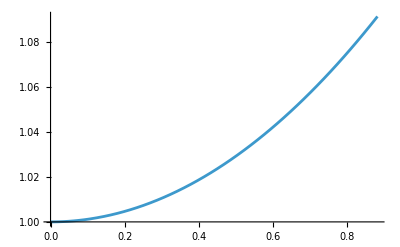

```mathematica
Plot[Flatten[L[r]/.Soln],{r,r0,end}]
```

```mathematica
LShift = (1/2 Log[1-(2*m[r])/r]-L[r])/.Soln[[1]]/.r->end
```

-1.24782

```mathematica
m[r]/.Soln[[1]]/.r->end
```

0.118552

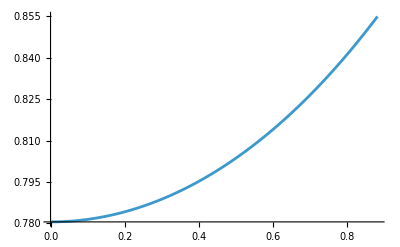

```mathematica
Plot[Exp[L[r]+LShift]/.Soln[[1]],{r,0,end}]
```

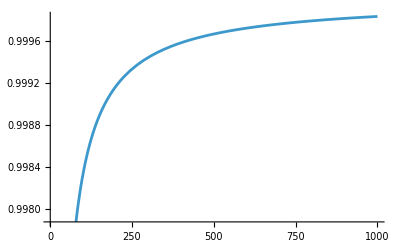

```mathematica
Plot[Exp[1/2 Log[1-(2*0.1664502149491048)/r]],{r,end,1000}]
```

## Formal Power Series Expansion for TOV Stars

```mathematica
SeriesSubs = {m'[r]->Subscript[a, 1]+2*Subscript[a, 2]*r+3 Subscript[a, 3]*r^2+4*Subscript[a, 4]*r^3+5*Subscript[a, 5]*r^4+6*Subscript[a, 6]*r^5+7*Subscript[a, 7]*r^6+8*Subscript[a, 8]*r^7+9*Subscript[a, 9]*r^8+10*Subscript[a, 10]*r^9+11*Subscript[a, 11]*r^10+O[r]^11,ρ'[r]->Subscript[b, 1]+2*Subscript[b, 2]*r+3 Subscript[b, 3]*r^2+4*Subscript[b, 4]*r^3+5*Subscript[b, 5]*r^4+6*Subscript[b, 6]*r^5+7*Subscript[b, 7]*r^6+8*Subscript[b, 8]*r^7+9*Subscript[b, 9]*r^8+10*Subscript[b, 10]*r^9+11*Subscript[b, 11]*r^10+O[r]^11,m[r]->Subscript[a, 1]*r+Subscript[a, 2]*r^2+Subscript[a, 3]*r^3+Subscript[a, 4]*r^4+Subscript[a, 5]*r^5+Subscript[a, 6]*r^6+Subscript[a, 7]*r^7+Subscript[a, 8]*r^8+Subscript[a, 9]*r^9+Subscript[a, 10]*r^10+O[r]^11,ρ[r]->Subscript[b, 0]+Subscript[b, 1]*r+Subscript[b, 2]*r^2+Subscript[b, 3]*r^3+Subscript[b, 4]*r^4+Subscript[b, 5]*r^5+Subscript[b, 6]*r^6+Subscript[b, 7]*r^7+Subscript[b, 8]*r^8+Subscript[b, 9]*r^9+Subscript[b, 10]*r^10+O[r]^11,L'[r]->Subscript[c, 1]+2*Subscript[c, 2]*r+3 Subscript[c, 3]*r^2+4*Subscript[c, 4]*r^3+5*Subscript[c, 5]*r^4+6*Subscript[c, 6]*r^5+7*Subscript[c, 7]*r^6+8*Subscript[c, 8]*r^7+9*Subscript[c, 9]*r^8+10*Subscript[c, 10]*r^9+11*Subscript[c, 11]*r^10+O[r]^11,L[r]->Subscript[c, 0]+Subscript[c, 1]*r+Subscript[c, 2]*r^2+Subscript[c, 3]*r^3+Subscript[c, 4]*r^4+Subscript[c, 5]*r^5+Subscript[c, 6]*r^6+Subscript[c, 7]*r^7+Subscript[c, 8]*r^8+Subscript[c, 9]*r^9+Subscript[c, 10]*r^10+O[r]^11}
```

{m'[r]→a_1+2 a_2 r+3 a_3 r^2+4 a_4 r^3+5 a_5 r^4+6 a_6 r^5+7 a_7 r^6+8 a_8 r^7+9 a_9 r^8+10 a_10 r^9+11 a_11 r^10+O[r]^11,ρ'[r]→b_1+2 b_2 r+3 b_3 r^2+4 b_4 r^3+5 b_5 r^4+6 b_6 r^5+7 b_7 r^6+8 b_8 r^7+9 b_9 r^8+10 b_10 r^9+11 b_11 r^10+O[r]^11,m[r]→a_1 r+a_2 r^2+a_3 r^3+a_4 r^4+a_5 r^5+a_6 r^6+a_7 r^7+a_8 r^8+a_9 r^9+a_10 r^10+O[r]^11,ρ[r]→b_0+b_1 r+b_2 r^2+b_3 r^3+b_4 r^4+b_5 r^5+b_6 r^6+b_7 r^7+b_8 r^8+b_9 r^9+b_10 r^10+O[r]^11,L'[r]→c_1+2 c_2 r+3 c_3 r^2+4 c_4 r^3+5 c_5 r^4+6 c_6 r^5+7 c_7 r^6+8 c_8 r^7+9 c_9 r^8+10 c_10 r^9+11 c_11 r^10+O[r]^11,L[r]→c_0+c_1 r+c_2 r^2+c_3 r^3+c_4 r^4+c_5 r^5+c_6 r^6+c_7 r^7+c_8 r^8+c_9 r^9+c_10 r^10+O[r]^11}

The series coefficients are determined by substituting into the TOV ODEs and solving for the coefficients

```mathematica
SeriesCoefficientConditionsM={Subscript[a, 1]->0,Subscript[a, 2]->0,Subscript[a, 3]->Subscript[b, 0]/6,Subscript[a, 4]->Subscript[b, 1]/8,Subscript[a, 5]->Subscript[b, 2]/10,Subscript[a, 6]->Subscript[b, 3]/12,Subscript[a, 7]->Subscript[b, 4]/14,Subscript[a, 8]->Subscript[b, 5]/16,Subscript[a, 9]->Subscript[b, 6]/18,Subscript[a, 10]->Subscript[b, 7]/20,Subscript[a, 11]->Subscript[b, 8]/22}
```

{a_1→0,a_2→0,a_3→b_0/6,a_4→b_1/8,a_5→b_2/10,a_6→b_3/12,a_7→b_4/14,a_8→b_5/16,a_9→b_6/18,a_10→b_7/20,a_11→b_8/22}

```mathematica
SeriesCoefficientConditionsRho={Subscript[b, 1]->0,Subscript[b, 2]->-((-1+(1+K) Subscript[b, 0]) (-3+(1+3 K) Subscript[b, 0]))/(12 K),Subscript[b, 3]->0,Subscript[b, 4]->1/(720 K^2)(-1+(1+K) Subscript[b, 0]) (-3+(1+3 K) Subscript[b, 0]) (-3 (3+5 K)+(4+3 K (3+5 K)) Subscript[b, 0]),Subscript[b, 5]->0,Subscript[b, 6]->-1/(181440 K^3)(-1+(1+K) Subscript[b, 0]) (-3+(1+3 K) Subscript[b, 0]) (9 (31+3 K (32+35 K))-18 (15+K (44+3 K (32+35 K))) Subscript[b, 0]+(61+K (200+3 K (206+9 K (32+35 K)))) Subscript[b, 0]^2),Subscript[b, 7]->0,Subscript[b, 8]->1/(65318400 K^4)(-1+(1+K) Subscript[b, 0]) (-3+(1+3 K) Subscript[b, 0]) (-9 (1261+3 K (1616+35 K (97+90 K)))+Subscript[b, 0] (9 (1924+K (6395+3 K (5528+105 K (97+90 K))))+Subscript[b, 0] (-8275-K (26222+3 K (30446+9 K (6908+105 K (97+90 K))))+(1258+K (4239+K (17936+3 K (12944+63 K (428+5 K (97+90 K)))))) Subscript[b, 0]))),Subscript[b, 9]->0}
```

{b_1→0,b_2→-((-1+(1+K) b_0) (-3+(1+3 K) b_0))/(12 K),b_3→0,b_4→1/(720 K^2)(-1+(1+K) b_0) (-3+(1+3 K) b_0) (-3 (3+5 K)+(4+3 K (3+5 K)) b_0),b_5→0,b_6→-1/(181440 K^3)(-1+(1+K) b_0) (-3+(1+3 K) b_0) (9 (31+3 K (32+35 K))-18 (15+K (44+3 K (32+35 K))) b_0+(61+K (200+3 K (206+9 K (32+35 K)))) b_0^2),b_7→0,b_8→1/(65318400 K^4)(-1+(1+K) b_0) (-3+(1+3 K) b_0) (-9 (1261+3 K (1616+35 K (97+90 K)))+b_0 (9 (1924+K (6395+3 K (5528+105 K (97+90 K))))+b_0 (-8275-K (26222+3 K (30446+9 K (6908+105 K (97+90 K))))+(1258+K (4239+K (17936+3 K (12944+63 K (428+5 K (97+90 K)))))) b_0))),b_9→0}

```mathematica
SeriesCoefficientConditionsL={Subscript[c, 1]->0,Subscript[c, 2]->1/12 (-3+(1+3 K) Subscript[b, 0]),Subscript[c, 3]->0,Subscript[c, 4]->-1/(1440 K)(-3+(1+3 K) Subscript[b, 0]) (-3 (1+5 K)+(3+K (-2+15 K)) Subscript[b, 0]),Subscript[c, 5]->0,Subscript[c, 6]->1/(181440 K^2)(-3+(1+3 K) Subscript[b, 0]) (9 (3+K (-2+35 K))+Subscript[b, 0] (-39+3 K (16+(47-210 K) K)+(12+K (-45+K (65+3 K (-41+105 K)))) Subscript[b, 0])),Subscript[c, 7]->0,Subscript[c, 8]->-1/(130636800 K^3)(-3+(1+3 K) Subscript[b, 0]) (-9 (155+3 K (-167+5 K (-109+315 K)))+Subscript[b, 0] (9 (305+K (-1364+3 K (-836+135 K (-16+35 K))))+Subscript[b, 0] (-1655+K (10655+3 K (2264+9 K (296+15 (179-315 K) K)))+(305+K (-2538+K (2875+3 K (-4532+9 K (373+5 K (-214+315 K)))))) Subscript[b, 0]))),Subscript[c, 9]->0}
```

{c_1→0,c_2→1/12 (-3+(1+3 K) b_0),c_3→0,c_4→-((-3+(1+3 K) b_0) (-3 (1+5 K)+(3+K (-2+15 K)) b_0))/(1440 K),c_5→0,c_6→1/(181440 K^2)(-3+(1+3 K) b_0) (9 (3+K (-2+35 K))+b_0 (-39+3 K (16+(47-210 K) K)+(12+K (-45+K (65+3 K (-41+105 K)))) b_0)),c_7→0,c_8→-1/(130636800 K^3)(-3+(1+3 K) b_0) (-9 (155+3 K (-167+5 K (-109+315 K)))+b_0 (9 (305+K (-1364+3 K (-836+135 K (-16+35 K))))+b_0 (-1655+K (10655+3 K (2264+9 K (296+15 (179-315 K) K)))+(305+K (-2538+K (2875+3 K (-4532+9 K (373+5 K (-214+315 K)))))) b_0))),c_9→0}

```mathematica
D[m[r],r]==r^2/2*ρ[r]/.SeriesSubs/.SeriesCoefficientConditionsM//FullSimplify
```

True

```mathematica
Solve[(-1/(16329600 K^3)(-27 (155-501 K-1635 K^2+4725 K^3)+18 (535-2064 K-5331 K^2-9810 K^3+28350 K^4) Subscript[b, 0]+6 (-1285+6001 K+13296 K^2+25002 K^3+44145 K^4-127575 K^5) Subscript[b, 0]^2+2 (1285-6652 K-15066 K^2-34578 K^3-33129 K^4-88290 K^5+255150 K^6) Subscript[b, 0]^3+(-305+1623 K+4739 K^2+4971 K^3+30717 K^4-1323 K^5+44145 K^6-127575 K^7) Subscript[b, 0]^4)+8 Subscript[c, 8])==0,Subscript[c, 8]]//FullSimplify
```

{{c_8→-1/(130636800 K^3)(-3+(1+3 K) b_0) (-9 (155+3 K (-167+5 K (-109+315 K)))+b_0 (9 (305+K (-1364+3 K (-836+135 K (-16+35 K))))+b_0 (-1655+K (10655+3 K (2264+9 K (296+15 (179-315 K) K)))+(305+K (-2538+K (2875+3 K (-4532+9 K (373+5 K (-214+315 K)))))) b_0)))}}

```mathematica
Collect[D[ρ[r],r]==1/K*(1-(K+1)*ρ[r])*(m[r]+r^3/2*(K*ρ[r]-1))/(r(r-2*m[r]))/.SeriesSubs/.SeriesCoefficientConditionsM/.SeriesCoefficientConditionsRho//FullSimplify,r]
```

True

```mathematica
D[L[r],r]==(m[r]+r^3/2*(K*ρ[r]-1))/(r(r-2*m[r]))/.SeriesSubs/.SeriesCoefficientConditionsM/.SeriesCoefficientConditionsRho/.SeriesCoefficientConditionsL//Simplify
```

True

Series Expansions up to r^5

ρ Series Expansions

```mathematica
RhoSeries = Collect[Normal[ρ[r]/.SeriesSubs/.SeriesCoefficientConditionsRho]/. r^b_/;b>=7->0//FullSimplify,r,FullSimplify]
FortranForm[%]
```

b_0-(r^2 (-1+(1+K) b_0) (-3+(1+3 K) b_0))/(12 K)+(r^4 (-1+(1+K) b_0) (-3+(1+3 K) b_0) (-3 (3+5 K)+(4+3 K (3+5 K)) b_0))/(720 K^2)-1/(181440 K^3)r^6 (-1+(1+K) b_0) (-3+(1+3 K) b_0) (9 (31+3 K (32+35 K))-18 (15+K (44+3 K (32+35 K))) b_0+(61+K (200+3 K (206+9 K (32+35 K)))) b_0^2)

Subscript(b,0) - (r**2*(-1 + (1 + K)*Subscript(b,0))*
     -     (-3 + (1 + 3*K)*Subscript(b,0)))/(12.*K) + 
     -  (r**4*(-1 + (1 + K)*Subscript(b,0))*(-3 + (1 + 3*K)*Subscript(b,0))*
     -     (-3*(3 + 5*K) + (4 + 3*K*(3 + 5*K))*Subscript(b,0)))/(720.*K**2) - 
     -  (r**6*(-1 + (1 + K)*Subscript(b,0))*(-3 + (1 + 3*K)*Subscript(b,0))*
     -     (9*(31 + 3*K*(32 + 35*K)) - 
     -       18*(15 + K*(44 + 3*K*(32 + 35*K)))*Subscript(b,0) + 
     -       (61 + K*(200 + 3*K*(206 + 9*K*(32 + 35*K))))*Subscript(b,0)**2))/
     -   (181440.*K**3)

M Series Expansion

```mathematica
MSeries = Collect[Normal[m[r]/.SeriesSubs/.SeriesCoefficientConditionsM/.SeriesCoefficientConditionsRho]/. r^b_/;b>=7->0//FullSimplify,r,FullSimplify]
FortranForm[%]
```

(r^3 b_0)/6-(r^5 (-1+(1+K) b_0) (-3+(1+3 K) b_0))/(120 K)

(r**3*Subscript(b,0))/6. - 
     -  (r**5*(-1 + (1 + K)*Subscript(b,0))*(-3 + (1 + 3*K)*Subscript(b,0)))/
     -   (120.*K)

L Series Expansion

```mathematica
LSeries = Collect[Normal[L[r]/.SeriesSubs/.SeriesCoefficientConditionsL]/. r^b_/;b>=7->0//FullSimplify,r,FullSimplify]
FortranForm[%]
```

1/12 r^2 (-3+(1+3 K) b_0)-(r^4 (-3+(1+3 K) b_0) (-3 (1+5 K)+(3+K (-2+15 K)) b_0))/(1440 K)+1/(181440 K^2)r^6 (-3+(1+3 K) b_0) (9 (3+K (-2+35 K))+b_0 (-39+3 K (16+(47-210 K) K)+(12+K (-45+K (65+3 K (-41+105 K)))) b_0))+c_0

(r**2*(-3 + (1 + 3*K)*Subscript(b,0)))/12. - 
     -  (r**4*(-3 + (1 + 3*K)*Subscript(b,0))*
     -     (-3*(1 + 5*K) + (3 + K*(-2 + 15*K))*Subscript(b,0)))/(1440.*K) + 
     -  (r**6*(-3 + (1 + 3*K)*Subscript(b,0))*
     -     (9*(3 + K*(-2 + 35*K)) + 
     -       Subscript(b,0)*(-39 + 3*K*(16 + (47 - 210*K)*K) + 
     -          (12 + K*(-45 + K*(65 + 3*K*(-41 + 105*K))))*Subscript(b,0))))/
     -   (181440.*K**2) + Subscript(c,0)

```mathematica
TeXForm[(-3+(-1+3 K) Subscript[b, 0]) (9 (-2+K (37+35 K))+Subscript[b, 0] (6-6 K^2 (286+105 K)+(12+K (-303+K (1313+3 K (461+105 K)))) Subscript[b, 0]))]
```

\left(b_0 (3 K-1)-3\right) \left(b_0 \left(b_0 (K (K (3 K (105
   K+461)+1313)-303)+12)-6 (105 K+286) K^2+6\right)+9 (K (35 K+37)-2)\right)

```mathematica
LSeries/.r->0.01/.Subscript[b, 0]->1.1/.K->1/.Subscript[c, 0]->1
```

1.00001

```mathematica
r0=0.01
Soln=NDSolve[{D[m[r],r]==r^2/2*ρ[r],D[L[r],r]==(m[r]-r^3/2*(K*ρ[r]-1))/(r(r-2*m[r])),D[ρ[r],r]==1/K*(1-(K+1)*ρ[r])*(m[r]-r^3/2*(K*ρ[r]-1))/(r(r-2*m[r])),m[r0]==1.8333253333333337*^-7,ρ[r0]==1.0999919998106626,L[r0]==1.0000066668688947,WhenEvent[ρ[r]==1/K,end=r;"StopIntegration"]}/.K->1,{m[r],L[r],ρ[r]},{r,r0,3}]
```

0.01

{{m[r]→InterpolatingFunction[…][r],L[r]→InterpolatingFunction[…][r],ρ[r]→InterpolatingFunction[…][r]}}

```mathematica
end
```

0.985239

```mathematica
L[r]/.Soln/.r->end
```

{1.09116}

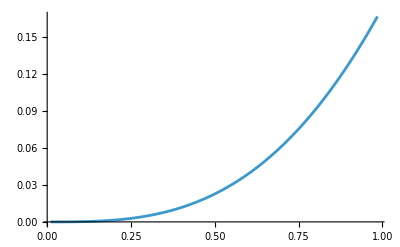

```mathematica
Plot[Flatten[m[r]/.Soln],{r,r0,end}]
```

## Perturbed TOV Star

```mathematica
HamiltonianEq
```

{A^(0,1)[t,r]→-(A[t,r] (-1+A[t,r]^2))/(2 r)+1/2 A[t,r]^3 r (p[t,r] (-1+Γ[t,r]^2)+Γ[t,r]^2 ρ[t,r])}

```mathematica
D[r[]/2*(1-1/A[t[],r[]]^2),r[]]/.HamiltonianEq//FullSimplify
```

1/2 r^2 (p[t,r] (-1+Γ[t,r]^2)+Γ[t,r]^2 ρ[t,r])